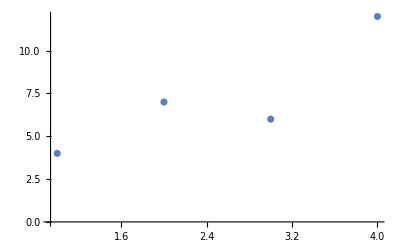

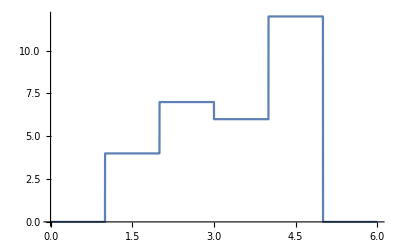

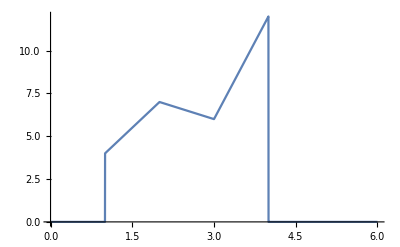

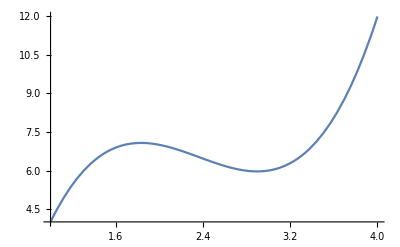

```mathematica
data={{1, 4}, {2, 7}, {3, 6}, {4, 12}};
ListPlot[data, PlotRange->Full]
f[x_]:=Piecewise[Table[{data[[i]][[2]], i<=x<i+1}, {i, 1, data//Length}]]
Plot[f[x], {x, 0, 6}, PlotRange->Full]
g[x_]:=Piecewise[Table[{(data[[i+1]][[2]]-data[[i]][[2]])/(data[[i+1]][[1]]-data[[i]][[1]]) (x-i)+data[[i]][[2]], i<=x<i+1}, {i, 1, (data//Length)-1}]]
Plot[g[x], {x, 0, 6}, PlotRange->Full]
Plot[InterpolatingPolynomial[data, x], {x, 1, 4}, PlotRange->Full]
```